```mathematica
Precision[tp_,fp_]=tp/(tp+fp)
```

Set::write: Tag Precision in Precision[tp_, fp_] is Protected.

tp/(fp+tp)

```mathematica
Clear[Precision]
```

Clear::wrsym: Symbol Precision is Protected.

```mathematica
Precision[1,1]
```

Precision::argx: Precision called with 2 arguments; 1 argument is expected.

Precision[1,1]

```mathematica
Clear[Precision]
```

Clear::wrsym: Symbol Precision is Protected.

```mathematica
IRPrecision[tp_,fp_]:=tp/(tp+fp)
```

```mathematica
IRPrecision[1,2]
```

1/3

```mathematica
TP[t_,m_,n_]:=Binomial[m,t]*n^(m-t)*(1-n)^t
```

```mathematica
FP[f_,m_,u_,v_]:=Binomial[u-m,f]*v^f*(1-v)^(u-m-f)
```

```mathematica
PMFFP[20,100,1000,.1]
```

2.18665×10^-20

```mathematica
PMF_FP[20,100,1000,0.1]
```

PMF_FP[20,100,1000,0.1]

```mathematica
IRExpPrecision[u_,m_,v_,n_]:=Sum[IRPrecision[t,f]*TP[t,m,n]*FP[f,m,u,v],{t,1,m},{f,0,u-m}]
```

```mathematica
IRExpPrecision[1000,100,.001,.001]
```

0.991158

```mathematica
IRExpPrecision[1000,500,.01]
```

0.990118

```mathematica
IRExpPrecision[u_,m_,v_]:=Sum[IRPrecision[m,f]*FP[f,m,u,v],{f,0,u-m}]
```

```mathematica
IRExpPrecisionTaylorApprox[u_,m_,v_,t_]:=t/(t+v(u-m))+t/(t+v(u-m))^3*(u-m)*v*(1-v)
```

```mathematica
IRExpPrecisionTaylorApprox[1000,500,.01,500]
```

0.990118

```mathematica
Simplify[D[IRPrecision[t,f],{{t,f},1}]]
```

{f/(f+t)^2,-t/(f+t)^2}

```mathematica
TeXForm[{-t/(f+t)^2+1/(f+t),-t/(f+t)^2}]
```

\left\{\frac{1}{f+t}-\frac{t}{(f+t)^2},-\frac{t}{(f+t)^2}\right\}

```mathematica
HessianPrecision[t_,f_]:=D[IRPrecision[t,f],{{t,f},2}]
```

```mathematica
Simplify[HessianPrecision[t,f]]
```

```mathematica
TeXForm[{{-(2 f)/(f+t)^3,(-f+t)/(f+t)^3},{(-f+t)/(f+t)^3,(2 t)/(f+t)^3}}]
```

\left(
\begin{array}{cc}
 -\frac{2 f}{(f+t)^3} & \frac{t-f}{(f+t)^3} \\
 \frac{t-f}{(f+t)^3} & \frac{2 t}{(f+t)^3} \\
\end{array}
\right)

```mathematica
GradientPrecision[t_,f_]:=D[IRPrecision[t,f],{{t,f},1}]
```

```mathematica
GradientPrecision[t,f]
```

{-t/(f+t)^2+1/(f+t),-t/(f+t)^2}

```mathematica
IRPrecision[t,f]+1/2*{T-t,F-f}.HessianPrecision[t,f].{T-t,F-f}
```

t/(f+t)+1/2 ((-t+T) ((-f+F) ((2 t)/(f+t)^3-1/(f+t)^2)+((2 t)/(f+t)^3-2/(f+t)^2) (-t+T))+(-f+F) ((2 (-f+F) t)/(f+t)^3+((2 t)/(f+t)^3-1/(f+t)^2) (-t+T)))

```mathematica
Simplify[t/(f+t)+1/2 ((-t+T) ((-f+F) ((2 t)/(f+t)^3-1/(f+t)^2)+((2 t)/(f+t)^3-2/(f+t)^2) (-t+T))+(-f+F) ((2 (-f+F) t)/(f+t)^3+((2 t)/(f+t)^3-1/(f+t)^2) (-t+T)))]
```

(f^2 (t+T)-f (F-2 t+T) (t+T)+t (F^2+t^2+F (-t+T)))/(f+t)^3

```mathematica
FullSimplify[-((-f+F) t)/(f+t)^2+t/(f+t)+(-t/(f+t)^2+1/(f+t)) (-t+T)+1/2 ((-t+T) ((-f+F) ((2 t)/(f+t)^3-1/(f+t)^2)+((2 t)/(f+t)^3-2/(f+t)^2) (-t+T))+(-f+F) ((2 (-f+F) t)/(f+t)^3+((2 t)/(f+t)^3-1/(f+t)^2) (-t+T)))]
```

(t (f-F+t)^2+(2 f^2-f F+2 f t+F t) T-f T^2)/(f+t)^3

```mathematica
Solve[(t (f-F+t)^2+(2 f^2-f F+2 f t+F t) T-f T^2)/(f+t)^3==0,t]
```

```mathematica
Simplify[%73]
```

(f^2 (t+2 T)+t (F^2+t^2+F (-2 t+T))-f (-2 t^2-2 t T+T^2+F (2 t+T)))/(f+t)^3

```mathematica
FullSimplify[(m(1-n))/(m(1-n)+(u-m)v)+((u-m)*v*m*(1-n)*n+m*(1-n)*(u-m)*v*(1-v))/(m(1-n)+(u-m)*v)^3,m<=u && n<.1 && n>=0&& v<.1 && v>0 &&n+v>0]
```

(m (1-n) (n (-m+u) v+(m-u) (-1+v) v+(u v-m (-1+n+v))^2))/(u v-m (-1+n+v))^3

```mathematica
Simplify[(m (1-n) (n (-m+u) v+(m-u) (-1+v) v+(u v-m (-1+n+v))^2))/(u v-m (-1+n+v))^3]
```

(m (1-n) (n (-m+u) v+(m-u) (-1+v) v+(u v-m (-1+n+v))^2))/(u v-m (-1+n+v))^3

```mathematica
FullSimplify[m (1-n) (n (-m+u) v+(m-u) (-1+v) v+(u v-m (-1+n+v))^2),m≤u && n<1 && n>0&& v<1 && v>0 && Element[u,Integers] && Element[m,Integers]]
```

m (1-n) (n (-m+u) v+(m-u) (-1+v) v+(u v-m (-1+n+v))^2)

```mathematica
Simplify[m^3/(u v-m (-1+n+v))^3-(3 m^3 n)/(u v-m (-1+n+v))^3+(3 m^3 n^2)/(u v-m (-1+n+v))^3-(m^3 n^3)/(u v-m (-1+n+v))^3-(m^2 v)/(u v-m (-1+n+v))^3-(2 m^3 v)/(u v-m (-1+n+v))^3+(4 m^3 n v)/(u v-m (-1+n+v))^3+(m^2 n^2 v)/(u v-m (-1+n+v))^3-(2 m^3 n^2 v)/(u v-m (-1+n+v))^3+(m u v)/(u v-m (-1+n+v))^3+(2 m^2 u v)/(u v-m (-1+n+v))^3-(4 m^2 n u v)/(u v-m (-1+n+v))^3-(m n^2 u v)/(u v-m (-1+n+v))^3+(2 m^2 n^2 u v)/(u v-m (-1+n+v))^3+(m^2 v^2)/(u v-m (-1+n+v))^3+(m^3 v^2)/(u v-m (-1+n+v))^3-(m^2 n v^2)/(u v-m (-1+n+v))^3-(m^3 n v^2)/(u v-m (-1+n+v))^3-(m u v^2)/(u v-m (-1+n+v))^3-(2 m^2 u v^2)/(u v-m (-1+n+v))^3+(m n u v^2)/(u v-m (-1+n+v))^3+(2 m^2 n u v^2)/(u v-m (-1+n+v))^3+(m u^2 v^2)/(u v-m (-1+n+v))^3-(m n u^2 v^2)/(u v-m (-1+n+v))^3]
```

(m (-1+n) (-m (n+2 n u+(-1+2 u) (-1+v)) v+m^2 (-1+n+v)^2+u v (1+n+(-1+u) v)))/(-u v+m (-1+n+v))^3

```mathematica
TeXForm[(m (1-n) (n (-m+u) v+(m-u) (-1+v) v+(u v-m (-1+n+v))^2))/(u v-m (-1+n+v))^3]
```

\frac{m (1-n) \left((u v-m (n+v-1))^2+n v (u-m)+(v-1) v (m-u)\right)}{(u v-m (n+v-1))^3}

```mathematica
IRExpPrecisionHessian[u_,m_,v_,n_]:=(m (1-n) (n (-m+u) v+(m-u) (-1+v) v+(u v-m (-1+n+v))^2))/(u v-m (-1+n+v))^3
```

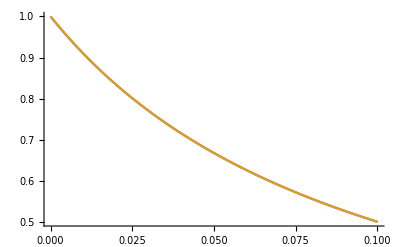

```mathematica
Plot[{IRExpPrecisionHessian[1000,100,v,.1],IRExpPrecision[1000,100,v,.1]},{v,.0000000000001,.1}]
```

```mathematica
Plot3D[IRExpPrecisionHessian[1000,100,v,n],{v,.00000000000000001,.5},{n,.00000000000000001,.5}]
```

-Graphics3D-

```mathematica
Plot3D[IRExpPrecisionHessian[1000,100,v,n],{v,1.*^-17,0.5},{n,1.*^-17,0.5},PlotTheme->"Monochrome"]
```

-Graphics3D-

```mathematica
Plot3D[IRExpPrecisionHessian[1000,100,v,n],{v,1.*^-17,0.5},{n,1.*^-17,0.5},PlotStyle->Directive[GrayLevel[0],Opacity[0.618]],PlotTheme->"Monochrome"]
```

-Graphics3D-

```mathematica
Plot3D[IRExpPrecisionHessian[100000,5000,v,n],{v,1.*^-17,0.05},{n,1.*^-17,0.2},Mesh->Automatic,MeshFunctions->{#3&},PlotStyle->Directive[GrayLevel[0],Opacity[0.8]],PlotTheme->"Monochrome"]
```

-Graphics3D-

```mathematica
Plot3D[IRExpPrecisionHessian[100000,5000,v,n],{v,1.*^-17,0.05},{n,1.*^-17,0.2},PlotPoints->100,MaxRecursion->9,Mesh->Automatic,MeshFunctions->{#3&},PlotStyle->Directive[GrayLevel[0],Opacity[0.8]],PlotTheme->"Monochrome"]
```

-Graphics3D-

```mathematica
Plot3D[IRExpPrecisionHessian[100000,5000,v,n],{v,1.*^-17,0.05},{n,1.*^-17,0.2},Mesh->Automatic,MeshStyle->Directive[GrayLevel[0],Opacity[0.152],AbsoluteThickness[1.52],Dashed],PlotPoints->100,MaxRecursion->9,MeshFunctions->{#3&},PlotStyle->Directive[GrayLevel[0],Opacity[0.8]],PlotTheme->"Monochrome"]
```

-Graphics3D-

```mathematica
Plot3D[IRExpPrecisionHessian[100000,5000,v,n],{v,1.*^-17,0.05},{n,1.*^-17,0.2},PlotPoints->12,MaxRecursion->1,Mesh->Automatic,MeshStyle->Directive[GrayLevel[0],Opacity[0.152],AbsoluteThickness[1.52],Dashed],PlotPoints->100,MaxRecursion->9,MeshFunctions->{#3&},PlotStyle->Directive[GrayLevel[0],Opacity[0.8]],PlotTheme->"Monochrome",AxesLabel->{ϵ,η,γ}]
```

-Graphics3D-

```mathematica
Plot3D[IRExpPrecisionHessian[100000,5000,v,n],{v,1.*^-17,0.05},{n,1.*^-17,0.2},Mesh->Automatic,MeshStyle->Directive[GrayLevel[0],Opacity[0.12],AbsoluteThickness[0.295]],PlotPoints->12,MaxRecursion->1,MeshFunctions->{#3&},PlotStyle->Directive[GrayLevel[0],Opacity[0.8]],PlotTheme->"Monochrome",AxesLabel->{ϵ,η,γ}]
```

-Graphics3D-

```mathematica
p1=Plot3D[IRExpPrecisionHessian[100000,5000,v,n],{v,1.*^-17,0.05},{n,1.*^-17,0.2},PlotTheme->"Monochrome",Mesh->Automatic,MeshStyle->Directive[GrayLevel[0],Opacity[0.12],AbsoluteThickness[0.295]],PlotPoints->12,MaxRecursion->1,MeshFunctions->{#3&},PlotStyle->Directive[GrayLevel[0],Opacity[0.8]],AxesLabel->{ϵ,η,γ}]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\Spinoza\\Desktop\\.svg",p1,"SVG"]
```

C:\Users\Spinoza\Desktop\.svg

```mathematica
datacsv3d=Table[{v,n,IRExpPrecisionHessian[1000,100,v,n]},{v,.00001,0.05,.005},{n,.00001,0.15,.01}]
```

{{{0.00001,0.00001,0.999911},{0.00001,0.01001,0.99991},{0.00001,0.02001,0.999909},{0.00001,0.03001,0.999908},{0.00001,0.04001,0.999907},{0.00001,0.05001,0.999906},{0.00001,0.06001,0.999905},{0.00001,0.07001,0.999904},{0.00001,0.08001,0.999903},{0.00001,0.09001,0.999902},{0.00001,0.10001,0.999901},{0.00001,0.11001,0.9999},{0.00001,0.12001,0.999899},{0.00001,0.13001,0.999898},{0.00001,0.14001,0.999897}},{{0.00501,0.00001,0.957248},{0.00501,0.01001,0.956843},{0.00501,0.02001,0.95643},{0.00501,0.03001,0.956008},{0.00501,0.04001,0.955579},{0.00501,0.05001,0.955141},{0.00501,0.06001,0.954695},{0.00501,0.07001,0.954239},{0.00501,0.08001,0.953775},{0.00501,0.09001,0.9533},{0.00501,0.10001,0.952816},{0.00501,0.11001,0.952322},{0.00501,0.12001,0.951817},{0.00501,0.13001,0.951302},{0.00501,0.14001,0.950775}},{{0.01001,0.00001,0.918043},{0.01001,0.01001,0.917297},{0.01001,0.02001,0.916538},{0.01001,0.03001,0.915764},{0.01001,0.04001,0.914976},{0.01001,0.05001,0.914173},{0.01001,0.06001,0.913354},{0.01001,0.07001,0.91252},{0.01001,0.08001,0.91167},{0.01001,0.09001,0.910802},{0.01001,0.10001,0.909918},{0.01001,0.11001,0.909016},{0.01001,0.12001,0.908095},{0.01001,0.13001,0.907156},{0.01001,0.14001,0.906197}},{{0.01501,0.00001,0.881896},{0.01501,0.01001,0.880863},{0.01501,0.02001,0.879811},{0.01501,0.03001,0.878741},{0.01501,0.04001,0.877651},{0.01501,0.05001,0.876542},{0.01501,0.06001,0.875412},{0.01501,0.07001,0.874261},{0.01501,0.08001,0.873089},{0.01501,0.09001,0.871895},{0.01501,0.10001,0.870678},{0.01501,0.11001,0.869437},{0.01501,0.12001,0.868173},{0.01501,0.13001,0.866883},{0.01501,0.14001,0.865569}},{{0.02001,0.00001,0.848466},{0.02001,0.01001,0.847189},{0.02001,0.02001,0.845891},{0.02001,0.03001,0.844571},{0.02001,0.04001,0.843227},{0.02001,0.05001,0.841861},{0.02001,0.06001,0.84047},{0.02001,0.07001,0.839054},{0.02001,0.08001,0.837613},{0.02001,0.09001,0.836146},{0.02001,0.10001,0.834652},{0.02001,0.11001,0.83313},{0.02001,0.12001,0.83158},{0.02001,0.13001,0.830001},{0.02001,0.14001,0.828392}},{{0.02501,0.00001,0.817459},{0.02501,0.01001,0.815976},{0.02501,0.02001,0.81447},{0.02501,0.03001,0.812938},{0.02501,0.04001,0.811381},{0.02501,0.05001,0.809798},{0.02501,0.06001,0.808188},{0.02501,0.07001,0.80655},{0.02501,0.08001,0.804884},{0.02501,0.09001,0.803188},{0.02501,0.10001,0.801463},{0.02501,0.11001,0.799708},{0.02501,0.12001,0.797921},{0.02501,0.13001,0.796101},{0.02501,0.14001,0.794249}},{{0.03001,0.00001,0.788623},{0.03001,0.01001,0.786966},{0.03001,0.02001,0.785283},{0.03001,0.03001,0.783573},{0.03001,0.04001,0.781836},{0.03001,0.05001,0.78007},{0.03001,0.06001,0.778276},{0.03001,0.07001,0.776451},{0.03001,0.08001,0.774597},{0.03001,0.09001,0.772711},{0.03001,0.10001,0.770793},{0.03001,0.11001,0.768843},{0.03001,0.12001,0.766859},{0.03001,0.13001,0.76484},{0.03001,0.14001,0.762786}},{{0.03501,0.00001,0.761739},{0.03501,0.01001,0.759935},{0.03501,0.02001,0.758103},{0.03501,0.03001,0.756242},{0.03501,0.04001,0.754353},{0.03501,0.05001,0.752433},{0.03501,0.06001,0.750484},{0.03501,0.07001,0.748503},{0.03501,0.08001,0.746491},{0.03501,0.09001,0.744446},{0.03501,0.10001,0.742367},{0.03501,0.11001,0.740254},{0.03501,0.12001,0.738107},{0.03501,0.13001,0.735923},{0.03501,0.14001,0.733702}},{{0.04001,0.00001,0.736618},{0.04001,0.01001,0.734688},{0.04001,0.02001,0.732729},{0.04001,0.03001,0.730741},{0.04001,0.04001,0.728724},{0.04001,0.05001,0.726676},{0.04001,0.06001,0.724596},{0.04001,0.07001,0.722484},{0.04001,0.08001,0.72034},{0.04001,0.09001,0.718162},{0.04001,0.10001,0.715949},{0.04001,0.11001,0.713702},{0.04001,0.12001,0.711418},{0.04001,0.13001,0.709098},{0.04001,0.14001,0.706739}},{{0.04501,0.00001,0.713091},{0.04501,0.01001,0.711055},{0.04501,0.02001,0.70899},{0.04501,0.03001,0.706895},{0.04501,0.04001,0.704769},{0.04501,0.05001,0.702613},{0.04501,0.06001,0.700424},{0.04501,0.07001,0.698203},{0.04501,0.08001,0.695948},{0.04501,0.09001,0.693659},{0.04501,0.10001,0.691336},{0.04501,0.11001,0.688976},{0.04501,0.12001,0.68658},{0.04501,0.13001,0.684147},{0.04501,0.14001,0.681675}}}

```mathematica
datamy=Flatten[datacsv3d,1]
```

{{0.00001,0.00001,0.999911},{0.00001,0.01001,0.99991},{0.00001,0.02001,0.999909},{0.00001,0.03001,0.999908},{0.00001,0.04001,0.999907},{0.00001,0.05001,0.999906},{0.00001,0.06001,0.999905},{0.00001,0.07001,0.999904},{0.00001,0.08001,0.999903},{0.00001,0.09001,0.999902},{0.00001,0.10001,0.999901},{0.00001,0.11001,0.9999},{0.00001,0.12001,0.999899},{0.00001,0.13001,0.999898},{0.00001,0.14001,0.999897},{0.00501,0.00001,0.957248},{0.00501,0.01001,0.956843},{0.00501,0.02001,0.95643},{0.00501,0.03001,0.956008},{0.00501,0.04001,0.955579},{0.00501,0.05001,0.955141},{0.00501,0.06001,0.954695},{0.00501,0.07001,0.954239},{0.00501,0.08001,0.953775},{0.00501,0.09001,0.9533},{0.00501,0.10001,0.952816},{0.00501,0.11001,0.952322},{0.00501,0.12001,0.951817},{0.00501,0.13001,0.951302},{0.00501,0.14001,0.950775},{0.01001,0.00001,0.918043},{0.01001,0.01001,0.917297},{0.01001,0.02001,0.916538},{0.01001,0.03001,0.915764},{0.01001,0.04001,0.914976},{0.01001,0.05001,0.914173},{0.01001,0.06001,0.913354},{0.01001,0.07001,0.91252},{0.01001,0.08001,0.91167},{0.01001,0.09001,0.910802},{0.01001,0.10001,0.909918},{0.01001,0.11001,0.909016},{0.01001,0.12001,0.908095},{0.01001,0.13001,0.907156},{0.01001,0.14001,0.906197},{0.01501,0.00001,0.881896},{0.01501,0.01001,0.880863},{0.01501,0.02001,0.879811},{0.01501,0.03001,0.878741},{0.01501,0.04001,0.877651},{0.01501,0.05001,0.876542},{0.01501,0.06001,0.875412},{0.01501,0.07001,0.874261},{0.01501,0.08001,0.873089},{0.01501,0.09001,0.871895},{0.01501,0.10001,0.870678},{0.01501,0.11001,0.869437},{0.01501,0.12001,0.868173},{0.01501,0.13001,0.866883},{0.01501,0.14001,0.865569},{0.02001,0.00001,0.848466},{0.02001,0.01001,0.847189},{0.02001,0.02001,0.845891},{0.02001,0.03001,0.844571},{0.02001,0.04001,0.843227},{0.02001,0.05001,0.841861},{0.02001,0.06001,0.84047},{0.02001,0.07001,0.839054},{0.02001,0.08001,0.837613},{0.02001,0.09001,0.836146},{0.02001,0.10001,0.834652},{0.02001,0.11001,0.83313},{0.02001,0.12001,0.83158},{0.02001,0.13001,0.830001},{0.02001,0.14001,0.828392},{0.02501,0.00001,0.817459},{0.02501,0.01001,0.815976},{0.02501,0.02001,0.81447},{0.02501,0.03001,0.812938},{0.02501,0.04001,0.811381},{0.02501,0.05001,0.809798},{0.02501,0.06001,0.808188},{0.02501,0.07001,0.80655},{0.02501,0.08001,0.804884},{0.02501,0.09001,0.803188},{0.02501,0.10001,0.801463},{0.02501,0.11001,0.799708},{0.02501,0.12001,0.797921},{0.02501,0.13001,0.796101},{0.02501,0.14001,0.794249},{0.03001,0.00001,0.788623},{0.03001,0.01001,0.786966},{0.03001,0.02001,0.785283},{0.03001,0.03001,0.783573},{0.03001,0.04001,0.781836},{0.03001,0.05001,0.78007},{0.03001,0.06001,0.778276},{0.03001,0.07001,0.776451},{0.03001,0.08001,0.774597},{0.03001,0.09001,0.772711},{0.03001,0.10001,0.770793},{0.03001,0.11001,0.768843},{0.03001,0.12001,0.766859},{0.03001,0.13001,0.76484},{0.03001,0.14001,0.762786},{0.03501,0.00001,0.761739},{0.03501,0.01001,0.759935},{0.03501,0.02001,0.758103},{0.03501,0.03001,0.756242},{0.03501,0.04001,0.754353},{0.03501,0.05001,0.752433},{0.03501,0.06001,0.750484},{0.03501,0.07001,0.748503},{0.03501,0.08001,0.746491},{0.03501,0.09001,0.744446},{0.03501,0.10001,0.742367},{0.03501,0.11001,0.740254},{0.03501,0.12001,0.738107},{0.03501,0.13001,0.735923},{0.03501,0.14001,0.733702},{0.04001,0.00001,0.736618},{0.04001,0.01001,0.734688},{0.04001,0.02001,0.732729},{0.04001,0.03001,0.730741},{0.04001,0.04001,0.728724},{0.04001,0.05001,0.726676},{0.04001,0.06001,0.724596},{0.04001,0.07001,0.722484},{0.04001,0.08001,0.72034},{0.04001,0.09001,0.718162},{0.04001,0.10001,0.715949},{0.04001,0.11001,0.713702},{0.04001,0.12001,0.711418},{0.04001,0.13001,0.709098},{0.04001,0.14001,0.706739},{0.04501,0.00001,0.713091},{0.04501,0.01001,0.711055},{0.04501,0.02001,0.70899},{0.04501,0.03001,0.706895},{0.04501,0.04001,0.704769},{0.04501,0.05001,0.702613},{0.04501,0.06001,0.700424},{0.04501,0.07001,0.698203},{0.04501,0.08001,0.695948},{0.04501,0.09001,0.693659},{0.04501,0.10001,0.691336},{0.04501,0.11001,0.688976},{0.04501,0.12001,0.68658},{0.04501,0.13001,0.684147},{0.04501,0.14001,0.681675}}

```mathematica
Export["mydata.csv",datamy,"CSV"]
```

mydata.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["mydata.csv"]]]
```

```mathematica
datacsv3d=Table[{v,.2,IRExpPrecisionHessian[10000,1000,v,.2]},{v,0,0.25,.005}]
```

{{0.,0.2,1.},{0.005,0.2,0.946817},{0.01,0.2,0.898998},{0.015,0.2,0.855772},{0.02,0.2,0.816507},{0.025,0.2,0.780684},{0.03,0.2,0.74787},{0.035,0.2,0.717701},{0.04,0.2,0.689869},{0.045,0.2,0.664114},{0.05,0.2,0.640212},{0.055,0.2,0.617969},{0.06,0.2,0.59722},{0.065,0.2,0.577817},{0.07,0.2,0.559635},{0.075,0.2,0.542562},{0.08,0.2,0.526499},{0.085,0.2,0.51136},{0.09,0.2,0.497067},{0.095,0.2,0.48355},{0.1,0.2,0.470749},{0.105,0.2,0.458609},{0.11,0.2,0.447078},{0.115,0.2,0.436113},{0.12,0.2,0.425672},{0.125,0.2,0.41572},{0.13,0.2,0.406222},{0.135,0.2,0.397149},{0.14,0.2,0.388472},{0.145,0.2,0.380166},{0.15,0.2,0.372207},{0.155,0.2,0.364575},{0.16,0.2,0.357249},{0.165,0.2,0.350212},{0.17,0.2,0.343447},{0.175,0.2,0.336939},{0.18,0.2,0.330672},{0.185,0.2,0.324634},{0.19,0.2,0.318812},{0.195,0.2,0.313196},{0.2,0.2,0.307774},{0.205,0.2,0.302537},{0.21,0.2,0.297475},{0.215,0.2,0.292579},{0.22,0.2,0.287842},{0.225,0.2,0.283256},{0.23,0.2,0.278814},{0.235,0.2,0.274508},{0.24,0.2,0.270334},{0.245,0.2,0.266285},{0.25,0.2,0.262355}}

```mathematica
fpratefixedfnrate=Flatten[datacsv3d,1]
```

{0.,0.005,1.,0.005,0.005,0.954819,0.01,0.005,0.913541,0.015,0.005,0.87568,0.02,0.005,0.84083,0.025,0.005,0.808646,0.03,0.005,0.778833,0.035,0.005,0.751138,0.04,0.005,0.725344,0.045,0.005,0.701262,0.05,0.005,0.678727,0.055,0.005,0.657595,0.06,0.005,0.637737,0.065,0.005,0.619044,0.07,0.005,0.601415,0.075,0.005,0.584761,0.08,0.005,0.569005,0.085,0.005,0.554075,0.09,0.005,0.539908,0.095,0.005,0.526448,0.1,0.005,0.513642,0.105,0.005,0.501444,0.11,0.005,0.489812,0.115,0.005,0.478707,0.12,0.005,0.468094,0.125,0.005,0.457942,0.13,0.005,0.448221,0.135,0.005,0.438903,0.14,0.005,0.429965,0.145,0.005,0.421384,0.15,0.005,0.413138,0.155,0.005,0.405209,0.16,0.005,0.397579,0.165,0.005,0.39023,0.17,0.005,0.383148,0.175,0.005,0.376319,0.18,0.005,0.369729,0.185,0.005,0.363365,0.19,0.005,0.357217,0.195,0.005,0.351274,0.2,0.005,0.345524,0.205,0.005,0.33996,0.21,0.005,0.334573,0.215,0.005,0.329353,0.22,0.005,0.324294,0.225,0.005,0.319388,0.23,0.005,0.314628,0.235,0.005,0.310008,0.24,0.005,0.305521,0.245,0.005,0.301163,0.25,0.005,0.296927}

```mathematica
Export["fpratefixedfnrate2.csv",datacsv3d,"CSV"]
```

fpratefixedfnrate2.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fpratefixedfnrate.csv"]]]
```

```mathematica
data=Table[{v,n,IRExpPrecisionHessian[10000,1000,v,n]},{v,0,0.25,.005},{n,0,0.25,.005}]
```

{{{0.,0.,1.},{0.,0.005,1.},{0.,0.01,1.},{0.,0.015,1.},{0.,0.02,1.},{0.,0.025,1.},{0.,0.03,1.},{0.,0.035,1.},{0.,0.04,1.},33,{0.,0.21,1.},{0.,0.215,1.},{0.,0.22,1.},{0.,0.225,1.},{0.,0.23,1.},{0.,0.235,1.},{0.,0.24,1.},{0.,0.245,1.},{0.,0.25,1.}},49,{1}}
 |  |  |  |

```mathematica
dataflat=Flatten[data,1]
```

{{0.,0.,1.},{0.,0.005,1.},{0.,0.01,1.},{0.,0.015,1.},{0.,0.02,1.},{0.,0.025,1.},{0.,0.03,1.},2587,{0.25,0.22,0.257487},{0.25,0.225,0.25626},{0.25,0.23,0.255029},{0.25,0.235,0.253793},{0.25,0.24,0.252554},{0.25,0.245,0.25131},{0.25,0.25,0.250062}}
 |  |  |  |

```mathematica
Export["fpratevsfnrate.csv",dataflat,"CSV"]
```

fpratevsfnrate.csv